```mathematica
EigenvaluesOf[T_,basis_]:=Eigenvalues [(T@@#&)/@basis];
```

```mathematica
(* Project the vector v onto the orthonormal basis e, in the inner-product space described by add, mult, and product. *)
project[add_,mult_,product_][v_,e_]:=
Fold[add,Table[mult[product[v,e[[i]]],e[[i]]],{i,1,Length[e]}]];
(* Perform the Gram-Schmidt algorithm to turn the provided basis into an orthonormal basis in the inner-product space described by add, mult, and product. *)
GramSchmidt[add_,mult_,product_][basis_]:=
Module[{GramSchmidtIter,Norm,
Project=project[add,mult,product],
N=Length[basis]},
Norm[v_]:=Sqrt[product[v,v]];
GramSchmidtIter[e_,i_]:=
If[i>N,e,
GramSchmidtIter[
With[{v=basis[[i]]},
Append[e,
With[{p=add[v,mult[-1,Project[v,e]]]},mult[1/Norm[p],p]]]],
i+1]];
GramSchmidtIter[{mult[1/Norm[basis[[1]]],basis[[1]]]},2]];
```

```mathematica
(* Return the closest polynomial approximation of the given degree to the given function from the inner-product space described by add, mult, and product *)
PolynomialApprox[degree_,add_,mult_,product_][f_]:=Module[{Basis=Table[Function[i,Function[x,x^i]][i],{i,0,degree}],Ortho=GramSchmidt[add,mult,product]},
project[add,mult,product][f,Ortho[Basis]]];
```

```mathematica
(* mult, add, and product describe an inner-product space of real-valued functions with input values from the set [-π,π]. *)
mult[a_,f_]:=Function[x,a (f[x])];
add[f_,g_]:=Function[x,f[x]+g[x]];
product[f_,g_]:=∫_-π^π f[x]g[x]ⅆx;

(* Gives a polynomial approximation to the fifth degree of the provided function. *)
Deg5Approx:=PolynomialApprox[5,add,mult,product];
```

0.99945 x-0.165838 x^3+0.00799858 x^5-0.000147741 x^7

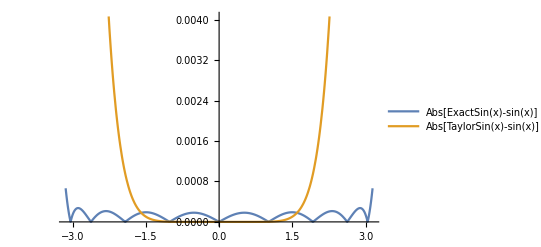

```mathematica
Clear[ExactSin,TaylorSin];
(* Get the approximated function as well as the corresponding taylor series *)
Expand[N[PolynomialApprox[7,add,mult,product][Sin][x]]]
ExactSin[x_]:=Evaluate[%];
TaylorSin[x_]:=x-x^3/6+x^5/120-x^7/5040;

(* Plot relative difference from sin to compare quality of approximation. *)
Plot[{Abs[ExactSin[x] - Sin[x]],Abs[TaylorSin[x]-Sin[x]]},{x,-Pi,Pi},PlotLegends->"Expressions"]
```